# hNB: Hexagonal Boron Nitride

Vectores primitivos

Dado que el nitruro de boro hexagonal (nHB) es un cristal bidimencionas con una estructurura hexagonal en cada uno de su clases de átomos podemos escribir ambos conjuntos de vectores primirivos en función del parámetro de red a y un desplazamiento d  de la siguiente forma

```mathematica
a = 1; (*largo de un lado de la red*)
v1 = a {1/2,(√3)/2}; v2 = a {-1/2,(√3)/2};  (*Vectores primitivos *)
d = 1/3(v1 + v2);       (* Desplazamiento: {0,a 1/(√3)};  o bien este valor en la base canónica *)
r[n1_,n2_,OptionsPattern[disp-> {0,0}]]:=N[OptionValue[disp]+ n1 v1 + n2 v2]  (* vectores de los átomos*)
```

Bravais Lattice

Primero se genera la para muchos puntos y estos puntos son guardados en listas; esto se hace para cada clase de átomos.

```mathematica
atomR1 = {}; atomR2 = {};                                                  (*Lista que no tiene nada para poder gurdar los datos*)
For[i=-5,i≤ 5,i++,   For[j=-5,j≤ 5,j++,
AppendTo[atomR1,Circle[r[i,j],.1]];                  (* átomos de la clase 1*)
AppendTo[atomR2,Circle[r[i,j,disp-> d],.1]]   (* átomos de la clase 2*)  ]]
```

```mathematica
{a1,a2} = Table[{Circle[r[i,j]],circle[r[i,j]]}, {i,-5,5},{j,-5,5}]
```

Después sólo le vamos a dar formato a la representación gráfica pero vamos a guardar la imagen para usarla más adelante. Al final se grafica la red y sobre ella se colocan los vectores primitivos.

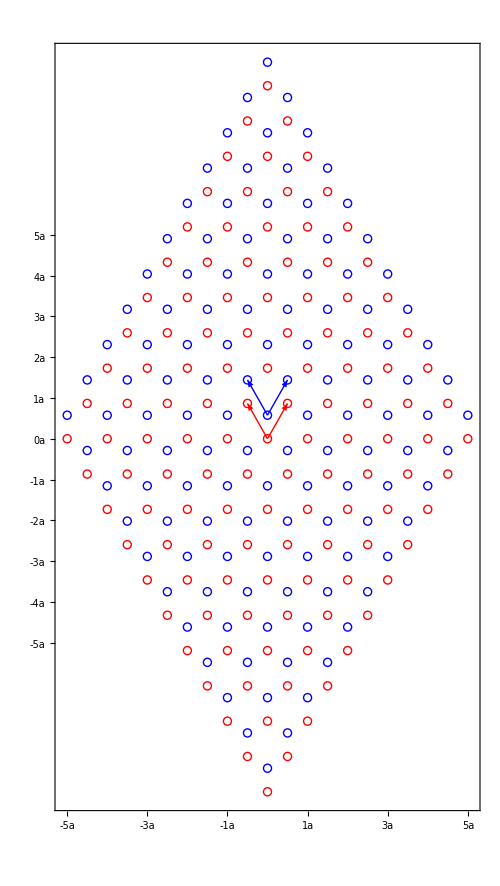

```mathematica
ticksX = Table[{i a , ToString[i]<>"a" },{i,-5,5,1}];
ticksY = ticksX;
cristalReal = Show[ Graphics[{Directive[Red,Thick],atomR1}], Graphics[{Directive[Blue,Thick],atomR2}],  (*Posición de los átomos*)
	 Frame-> True, FrameTicks-> {ticksX,ticksY},FrameStyle->Directive[Black,Thick,FontSize->15],   (*Maquillaje del dibujo*)
	ImageSize-> 500,PlotRange-> 3 a];    (*Tamaño y qué porsión de la imagen se vaa mostrar*)
Show[cristalReal,
 Graphics[{Directive[Red,Thick],Arrow[{r[0,0],r[1,0]}],Arrow[{r[0,0],r[0,1]}]}],
 Graphics[{Directive[Blue,Thick],Arrow[{r[0,0, disp-> d],r[1,0, disp-> d]}],Arrow[{r[0,0, disp-> d],r[0,1, disp-> d]}]}]]
```

Celda primitiva y de Wigner - Seitz

Esta es la celda con la que se puede generar todo el espacio  sól debe cumplir, además de esto, que no lo haga em.08almándose sobre sí misma. La celda convencional es cualquiera que cumpla esta propiedad yla de Wigner - Seitz lo que hace es que considera los primeros vecionos y se toma la distancia media entre el origen y estos y luego se trazan lineas perpendiculares: las intersecciones son squellas en donde los aristeas de las celda se lacalizan. El código que resuelve las ecuaciones de lineas paramétricas es

```mathematica
puntosWS[vecinos_]:= Module[{vec = vecinos, interseccion, max,dvecx,dvecy,vecxy,perp,ptsinter,i},
 max = Length[vec];interseccion = Table[0,{i,max}]; perp = Table[0,{i,max}];ptsinter = Table[0,{i,max}];
For[i=1,i≤ max, i++,
dvecx = 1/2(vec[[i,1]]-vec[[Mod[i+1,max,1],1]]);
dvecy = 1/2(vec[[i,2]]-vec[[Mod[i+1,max,1],2]]);
If[vec[[Mod[i+1,max,1],2]] ==0, 
	interseccion[[i]] = dvecx / vec[[i,2]],
	vecxy  = vec[[Mod[i+1,max,1],1]]/vec[[Mod[i+1,max,1],2]];
	interseccion[[i]] = (dvecy + vecxy dvecx)/(-vec[[i,1]] + vecxy vec[[i,2]])];
perp[[i]] = {-vec[[i,2]], vec[[i,1]]};
ptsinter[[i]] = 1/2 vec[[i]] + interseccion[[i]] * perp[[i]]  ];
{interseccion,ptsinter}] (*El resultado da el valor del parámetro endonde se evalua la curva y el otro es el punto en donde se encuentra.*)
```

```mathematica
uniCoordenadas = {{0,0},{1,0},{0,1},{-1,1},{-1,0},{0,-1},{1,-1}}; (* unitaria = Circle[r[#[[1]],#[[2]]],.1]&/@uni; Esa es la unitaria  que podemos dibujar *)
prim = r[#[[1]],#[[2]]] &/@Drop[uniCoordenadas,1]; (*las esquinas de los primeros vecinos*)
```

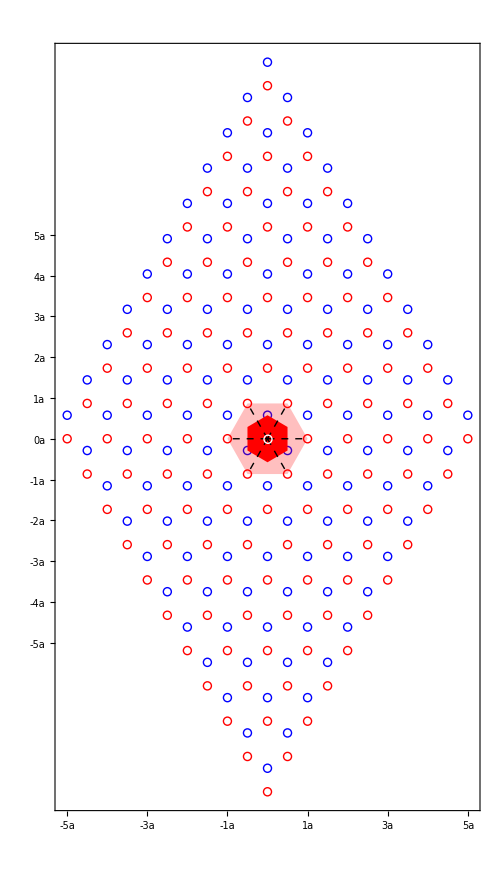

```mathematica
{ts,wigner}=puntosWS[prim];

Show[cristalReal,Graphics[{Directive[Red,Opacity[.25]],Polygon[prim]}],  (*Red y en sime la unitaria convencional*)
Graphics[{Directive[Red,Opacity[1]],Polygon[wigner]}],Graphics[{Directive[Thick,Dashed],Line[Append[{r[0,0]},#]&/@prim]}], (*Wigner y dist a 1os vecinos*)
Graphics[{Directive[White,Thick],Circle[r[0,0],.1]}], (*Sólo pone la que está en el origen que se tapó *)
PlotRange-> 2 a]
```

```mathematica
planosRed[t_, vecino_]:=vecino/2 + t {-vecino[[2]], vecino[[1]] }(*planos respecto al punto medio entre vecinos como función paramétrica*)
```

Reciprocal Lattice

En este caso queremos encontrar las K⃗ tales que cumplan que exp(iK⃗·(r⃗+R⃗))=exp(iK⃗·r⃗) , donde r⃗es un vector cualquiera y R⃗ es uno de la red de Bravais. esto se traduce en exp(K⃗·R⃗)=1 entonces si {(v⃗)_1,(v⃗)_2} es la base escogido de la red de Bravai y {(u⃗)_1,(u⃗)_(2}) la de la recíproca, se busca resiltver el sistema de ecuaciones (v⃗)_i·(u⃗)_j= 2 πδ_ij. Este tiene como solución (mediante una sustitución chafita) que
(u_(1x),u_(2x)) = (2 π)/Δ(v_(2y),-v_(2x))  y que (u_(1x),u_(2x)) = (2 π)/Δ(-v_(1y),v_(1x)) ; con Δ = det(v_(1x) | v_(2x)
v_(1y) | v_(2y))
Calculando todo esto en términos de los vectores v1 y v2  obtenemos el vector k, dado por

```mathematica
Δ = Det[{v1,v2}];
u1 = (2π)/Δ{v2[[2]], - v2[[1]]};
u2 = (2π)/Δ{-v1[[2]],  v1[[1]]};
k0 = 1/3(u1 + u2);
k[l_,m_, OptionsPattern[disp-> {0,0}]]:= N[ OptionValue[disp] + l u1 + m u2 ]
```

Otra vez generamos la lista de las posiciones de los puntos (sólo que ahora están en el espacio recóproco)

```mathematica
atomK1 = {};                                            (*Lista que no tiene nada para poder gurdar los datos*)
For[i=-5,i≤ 5,i++,   For[j=-5,j≤ 5,j++,
AppendTo[atomK1,Circle[k[i,j],.1  2π]];                  (* átomos de la clase 1*)  ]]
```

Y les volvemos a dar formatito para presentarlas. Es equivalente a lo que se hizo anteriormente en el espaico real.

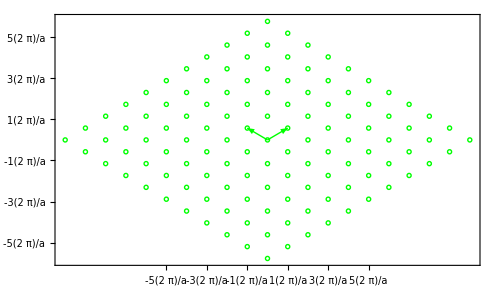

```mathematica
ticksX = Table[{(i 2π)/a , ToString[i]<>"(2  π)/a" },{i,-5,5,1}];
ticksY = ticksX;
cristalK = Show[ Graphics[{Directive[Green,Thick],atomK1}],   (*Posición de los átomos*)
	 Frame-> True, FrameTicks-> {ticksX,ticksY},FrameStyle->Directive[Black,Thick,FontSize->15],   (*Maquillaje del dibujo*)
	ImageSize-> 500,PlotRange-> 3(2 π/ a)];    (*Tamaño y qué porsión de la imagen se vaa mostrar*)
Show[cristalK,  Graphics[{Directive[Green,Thick],Arrow[{k[0,0],k[1,0]}],Arrow[{k[0,0],k[0,1]}]}]]
```

Primera zona de  Brillouin

Es exactamente la celda de Wigner - Seitz sólo que contruida en el espacio recíproco

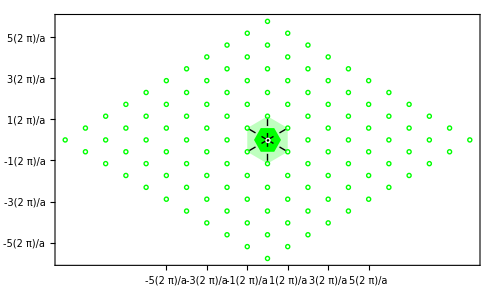

```mathematica
uniCoordenadas = {{0,0},{1,0},{1,1},{0,1},{-1,0},{-1,-1},{0,-1}}; (* unitaria = Circle[r[#[[1]],#[[2]]],.1]&/@uni; Esa es la unitaria  que podemos dibujar *)
primK = k[#[[1]],#[[2]] ]-k[0,0] &/@Drop[uniCoordenadas,1] ;(*Da los vectores que van a todos los vertices de la unitaria*)
{tsk,brillouin}=puntosWS[primK];

Show[cristalK,Graphics[{Directive[Green,Opacity[.25]],Polygon[primK]}],  (*Red y en sime la unitaria convencional*)
Graphics[{Directive[Green,Opacity[1]],Polygon[brillouin]}],Graphics[{Directive[Thick,Dashed],Line[Append[{k[0,0]},#]&/@primK]}], (*Wigner y dist a 1os vecinos*)
Graphics[{Directive[White,Thick],Circle[k[0,0],.1 2 π]}], (*Sólo pone la que está en el origen que se tapó *)
PlotRange-> 2 (2π/a)]
```

```mathematica
uniCoordenadas1 = {{0,0},{1,0},{1,1},{0,1},{-1,0},{-1,-1},{0,-1}}; (* unitaria = Circle[r[#[[1]],#[[2]]],.1]&/@uni; 
Esa es la unitaria  que podemos dibujar *)
uniCoordenadas2 = {{0,0},{1,0},{0,1},{-1,1},{-1,0},{0,-1},{1,-1}};
primK = k[#[[1]],#[[2]] ]-k[0,0] &/@Drop[uniCoordenadas,1] ;(*Da los vectores que van a todos los vertices de la unitaria*)
{tsk,brillouin}=puntosWS[primK];
cosa = Show[cristalK, Graphics[{Directive[Thick,Dashed],Line[Append[{k[0,0]},#]&/@primK]}]  ];

imagenes = {0,0,0,0,0};

For[i=1, i≤ 5, i++,
If[Mod[i,2]==1,vecino = i* uniCoordenadas1, vecino = i* uniCoordenadas2 ];
primK = k[#[[1]],#[[2]] ]-k[0,0] &/@Drop[vecino,1] ;(*Da los vectores que van a todos los vertices de la unitaria*)
{tsk,brillouin}=puntosWS[primK];
 Graphics[{Directive[Green,Opacity[.25]],Polygon[brillouin]}]  ;   ]
imagenes
```

{1,2,3,4,5}

```mathematica
imagenes = {0,0,0,0,0};

For[i=1, i≤ 5, i++,
If[Mod[i,2]==1,vecino = i* uniCoordenadas1, vecino = i* uniCoordenadas2 ];
primK = k[#[[1]], #[[2]]]-k[0,0] &/@Drop[vecino,1];
{tsk,brillouin}=puntosWS[primK];
imagenes[[i]] =  Graphics[{Directive[Green,Opacity[.1]],Polygon[brillouin]}] 
   ]
```

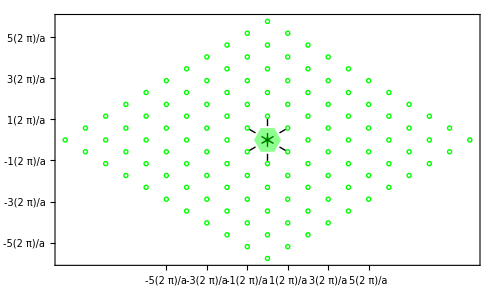

```mathematica
cosa
```